```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Dies ist die analytisch bestimmte Variante, sie stimmt aber, Stand jetzt, nicht.*)
```

```mathematica
Ω0s=Sqrt[(B1/2)^2+(δBz/2+A/2)^2]
Ω1s=Sqrt[(B1/2)^2+(δBz/2)^2]
```

√(B1^2/4+(A/2+δBz/2)^2)

√(B1^2/4+δBz^2/4)

```mathematica
FavAna=1/5(Cos[Ω0 *t]^2*Cos[A/2*t+δBz/2*t]^2
+Sin[Ω0 *t]^2*Sin[A/2*t+δBz/2*t]^2*((δBz+A)/(2*Ω0))^2
+Sin[Ω1 *t]^2*(B1/(2*Ω1))^2*Cos[δBz/2*t]^2
+1/2*Sin[2*Ω0 *t]*Sin[A*t+δBz*t]*((δBz+A)/(2*Ω0))
+2*Cos[Ω0 *t]*Cos[A/2*t+δBz/2*t]*Sin[Ω1 *t]*(B1/(2*Ω1))*Cos[δBz/2*t]
+2*Sin[Ω0 *t]*Sin[A/2*t+δBz/2*t]*Sin[Ω1 *t]*(B1/(2*Ω1))*((δBz+A)/(2*Ω0))*Cos[δBz/2*t] +1)/.{Ω0->Ω0s,Ω1->Ω1s};
```

```mathematica
FavTest= FavAna/.{t->(π/B1),A->2.2}//FullSimplify
```

$Aborted

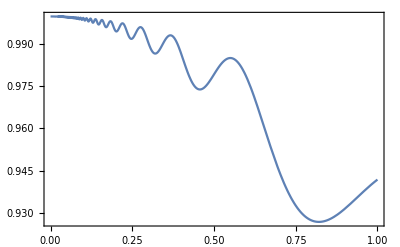

```mathematica
Plot[FavTest1,{B1,0,1},Frame->True]
```

```mathematica
(*Kontrolliere analytische Loesung mit Numerik*)
```

```mathematica
H=({{0, B1/2, 0, 0}, {B1/2, -(A+δBz), 0, 0}, {0, 0, 0, B1/2}, {0, 0, B1/2, -δBz}}); H0=({{0, 0, 0, 0}, {0, -(A+δBz), 0, 0}, {0, 0, 0, 0}, {0, 0, 0, -δBz}});
```

```mathematica
U=MatrixExp[-I t H] //FullSimplify;
U//MatrixForm
```

(ⅇ^(1/2 ⅈ t (A+δBz)) (Cos[1/2 t √(B1^2+(A+δBz)^2)]-(ⅈ (A+δBz) Sin[1/2 t √(B1^2+(A+δBz)^2)])/(√(B1^2+(A+δBz)^2))) | -(ⅈ B1 ⅇ^(1/2 ⅈ t (A+δBz)) Sin[1/2 t √(B1^2+(A+δBz)^2)])/(√(B1^2+(A+δBz)^2)) | 0 | 0
-(ⅈ B1 ⅇ^(1/2 ⅈ t (A+δBz)) Sin[1/2 t √(B1^2+(A+δBz)^2)])/(√(B1^2+(A+δBz)^2)) | ⅇ^(1/2 ⅈ t (A+δBz)) (Cos[1/2 t √(B1^2+(A+δBz)^2)]+(ⅈ (A+δBz) Sin[1/2 t √(B1^2+(A+δBz)^2)])/(√(B1^2+(A+δBz)^2))) | 0 | 0
0 | 0 | ⅇ^((ⅈ t δBz)/2) (Cos[1/2 t √(B1^2+δBz^2)]-(ⅈ δBz Sin[1/2 t √(B1^2+δBz^2)])/(√(B1^2+δBz^2))) | -(ⅈ B1 ⅇ^((ⅈ t δBz)/2) Sin[1/2 t √(B1^2+δBz^2)])/(√(B1^2+δBz^2))
0 | 0 | -(ⅈ B1 ⅇ^((ⅈ t δBz)/2) Sin[1/2 t √(B1^2+δBz^2)])/(√(B1^2+δBz^2)) | ⅇ^((ⅈ t δBz)/2) (Cos[1/2 t √(B1^2+δBz^2)]+(ⅈ δBz Sin[1/2 t √(B1^2+δBz^2)])/(√(B1^2+δBz^2))))

```mathematica
Uc=U/.t->π/B1//FullSimplify;
Uc//MatrixForm
```

(ⅇ^((ⅈ π (A+δBz))/(2 B1)) (Cos[(π √(B1^2+(A+δBz)^2))/(2 B1)]-(ⅈ (A+δBz) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2))) | -(ⅈ B1 ⅇ^((ⅈ π (A+δBz))/(2 B1)) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2)) | 0 | 0
-(ⅈ B1 ⅇ^((ⅈ π (A+δBz))/(2 B1)) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2)) | ⅇ^((ⅈ π (A+δBz))/(2 B1)) (Cos[(π √(B1^2+(A+δBz)^2))/(2 B1)]+(ⅈ (A+δBz) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2))) | 0 | 0
0 | 0 | ⅇ^((ⅈ π δBz)/(2 B1)) (Cos[(π √(B1^2+δBz^2))/(2 B1)]-(ⅈ δBz Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))) | -(ⅈ B1 ⅇ^((ⅈ π δBz)/(2 B1)) Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))
0 | 0 | -(ⅈ B1 ⅇ^((ⅈ π δBz)/(2 B1)) Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2)) | ⅇ^((ⅈ π δBz)/(2 B1)) (Cos[(π √(B1^2+δBz^2))/(2 B1)]+(ⅈ δBz Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))))

```mathematica
Transpose[Conjugate[Uc]].Uc//ComplexExpand//Simplify//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Rzn=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, I, 0}, {0, 0, 0, I}});
```

```mathematica
Uc2=Rzn . Uc//Simplify;
Uc2//MatrixForm
```

(ⅇ^((ⅈ π (A+δBz))/(2 B1)) (Cos[(π √(B1^2+(A+δBz)^2))/(2 B1)]-(ⅈ (A+δBz) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2))) | -(ⅈ B1 ⅇ^((ⅈ π (A+δBz))/(2 B1)) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2)) | 0 | 0
-(ⅈ B1 ⅇ^((ⅈ π (A+δBz))/(2 B1)) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2)) | ⅇ^((ⅈ π (A+δBz))/(2 B1)) (Cos[(π √(B1^2+(A+δBz)^2))/(2 B1)]+(ⅈ (A+δBz) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2))) | 0 | 0
0 | 0 | ⅈ ⅇ^((ⅈ π δBz)/(2 B1)) (Cos[(π √(B1^2+δBz^2))/(2 B1)]-(ⅈ δBz Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))) | (B1 ⅇ^((ⅈ π δBz)/(2 B1)) Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))
0 | 0 | (B1 ⅇ^((ⅈ π δBz)/(2 B1)) Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2)) | ⅈ ⅇ^((ⅈ π δBz)/(2 B1)) (Cos[(π √(B1^2+δBz^2))/(2 B1)]+(ⅈ δBz Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))))

```mathematica
U0=MatrixExp[-I t0 H0] /.t0->-π/B1//Simplify;
U0//MatrixForm
```

(1 | 0 | 0 | 0
0 | ⅇ^(-(ⅈ π (A+δBz))/B1) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(-(ⅈ π δBz)/B1))

```mathematica
Uc3=U0.Uc2//FullSimplify;
Uc3//MatrixForm
```

(ⅇ^((ⅈ π (A+δBz))/(2 B1)) (Cos[(π √(B1^2+(A+δBz)^2))/(2 B1)]-(ⅈ (A+δBz) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2))) | -(ⅈ B1 ⅇ^((ⅈ π (A+δBz))/(2 B1)) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2)) | 0 | 0
-(ⅈ B1 ⅇ^(-(ⅈ π (A+δBz))/(2 B1)) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2)) | ⅇ^(-(ⅈ π (A+δBz))/(2 B1)) (Cos[(π √(B1^2+(A+δBz)^2))/(2 B1)]+(ⅈ (A+δBz) Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2))) | 0 | 0
0 | 0 | ⅈ ⅇ^((ⅈ π δBz)/(2 B1)) (Cos[(π √(B1^2+δBz^2))/(2 B1)]-(ⅈ δBz Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))) | (B1 ⅇ^((ⅈ π δBz)/(2 B1)) Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))
0 | 0 | (B1 ⅇ^(-(ⅈ π δBz)/(2 B1)) Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2)) | ⅈ ⅇ^(-(ⅈ π δBz)/(2 B1)) (Cos[(π √(B1^2+δBz^2))/(2 B1)]+(ⅈ δBz Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))))

```mathematica
Ucnot=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
FavNum=(Abs[Tr[Ucnot.Uc3]]^2+4)/20//FullSimplify
```

$Aborted

```mathematica
FavNum=1/5 (1+Abs[Cos[(π (A+δBz))/(2 B1)] Cos[(π √(B1^2+(A+δBz)^2))/(2 B1)]+(B1 Cos[(π δBz)/(2 B1)] Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))+((A+δBz) Sin[(π (A+δBz))/(2 B1)] Sin[(π √(B1^2+(A+δBz)^2))/(2 B1)])/(√(B1^2+(A+δBz)^2))]^2);
```

```mathematica
FavTest1= FavAna/.{t->(π/B1),A->2.2,δBz->1};
FavTest2= FavNum/.{A->2.2,δBz->1};
```

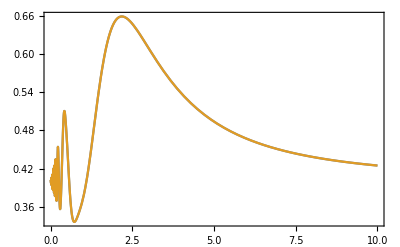

```mathematica
Plot[{FavTest1,FavTest2},{B1,0,10},Frame->True]
```

```mathematica
(*passt!!*)
(*Jetzt: Integration mit Gaussverteilung*)
```

```mathematica
FavNoisy1=FavNum*1/Sqrt[2*π*σ^2]*Exp[-1/2*(δBz/σ)^2]/.t->(π/B1);
```

```mathematica
FavNoisy2=FavNoisy1/.{A->2.2,B1->0.02,σ->0.5}
```

0.159577 ⅇ^(-2. δBz^2) (1+Abs[Cos[78.5398 (2.2+δBz)] Cos[78.5398 √(0.0004+(2.2+δBz)^2)]+(0.02 Cos[78.5398 δBz] Sin[78.5398 √(0.0004+δBz^2)])/(√(0.0004+δBz^2))+((2.2+δBz) Sin[78.5398 (2.2+δBz)] Sin[78.5398 √(0.0004+(2.2+δBz)^2)])/(√(0.0004+(2.2+δBz)^2))]^2)

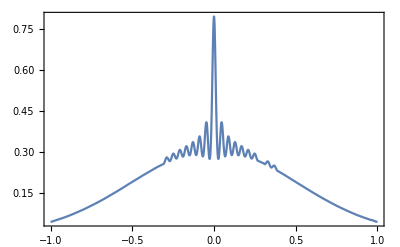

```mathematica
Plot[FavNoisy2,{δBz,-1.0,1.0},Frame->True]
```

```mathematica
NIntegrate[FavNoisy2,{δBz,-5,5}]
```

0.413096

```mathematica
FavNoisy3=FavNoisy1/.{A->2.2,σ->0.70710}
```

0.112839 ⅇ^(-1.00002 δBz^2) (1+Abs[Cos[(π (2.2+δBz))/(2 B1)] Cos[(π √(B1^2+(2.2+δBz)^2))/(2 B1)]+(B1 Cos[(π δBz)/(2 B1)] Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))+((2.2+δBz) Sin[(π (2.2+δBz))/(2 B1)] Sin[(π √(B1^2+(2.2+δBz)^2))/(2 B1)])/(√(B1^2+(2.2+δBz)^2))]^2)

```mathematica
test= Table[{B1,NIntegrate[FavNoisy3,{δBz,-5,5}]},{B1,0.01,0.5,.01}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in δBz near {δBz} = {0.0193758}. NIntegrate obtained 0.404662 and 7.87139×10^-6 for the integral and error estimates.

{{0.01,0.404662},{0.02,0.409243},{0.03,0.413737},{0.04,0.418149},{0.05,0.422484},{0.06,0.426735},{0.07,0.430907},{0.08,0.435007},{0.09,0.43904},{0.1,0.442999},{0.11,0.446885},{0.12,0.450701},{0.13,0.454411},{0.14,0.458114},{0.15,0.461719},{0.16,0.465284},{0.17,0.468715},{0.18,0.472243},{0.19,0.475537},{0.2,0.478782},{0.21,0.482155},{0.22,0.485407},{0.23,0.488423},{0.24,0.491396},{0.25,0.49449},{0.26,0.497644},{0.27,0.500692},{0.28,0.503534},{0.29,0.506206},{0.3,0.508822},{0.31,0.511488},{0.32,0.51425},{0.33,0.517087},{0.34,0.51993},{0.35,0.522703},{0.36,0.525349},{0.37,0.527842},{0.38,0.530187},{0.39,0.532417},{0.4,0.534575},{0.41,0.536709},{0.42,0.538859},{0.43,0.541054},{0.44,0.54331},{0.45,0.545629},{0.46,0.548004},{0.47,0.550419},{0.48,0.552854},{0.49,0.555284},{0.5,0.55769}}

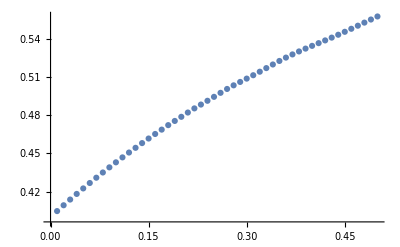

```mathematica
ListPlot[test]
```

```mathematica
Export["fileT2_2mus.dat", test]
```

fileT2_2mus.dat

```mathematica
FavNoisy4=FavNoisy1/.{A->2.2,σ->0.0156}
test2= Table[{B1,NIntegrate[FavNoisy4,{δBz,-5,5}]},{B1,0.01,0.5,.01}]
```

5.11464 ⅇ^(-2054.57 δBz^2) (1+Abs[Cos[(π (2.2+δBz))/(2 B1)] Cos[(π √(B1^2+(2.2+δBz)^2))/(2 B1)]+(B1 Cos[(π δBz)/(2 B1)] Sin[(π √(B1^2+δBz^2))/(2 B1)])/(√(B1^2+δBz^2))+((2.2+δBz) Sin[(π (2.2+δBz))/(2 B1)] Sin[(π √(B1^2+(2.2+δBz)^2))/(2 B1)])/(√(B1^2+(2.2+δBz)^2))]^2)

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in δBz near {δBz} = {-0.000155416}. NIntegrate obtained 0.563448 and 0.000092138 for the integral and error estimates.

{0.563448,0.687184,0.787053,0.852681,0.894345,0.921184,0.939312,0.951935,0.96099,0.967936,0.972998,0.976606,0.978668,0.982092,0.982937,0.985579,0.984845,0.987777,0.987977,0.986485,0.988455,0.990638,0.989478,0.987085,0.986843,0.989,0.991265,0.991563,0.989617,0.986667,0.984309,0.983552,0.984503,0.986553,0.988783,0.990344,0.990695,0.989678,0.98747,0.984468,0.981156,0.978001,0.975374,0.973521,0.972551,0.972458,0.973137,0.974423,0.976112,0.977991}

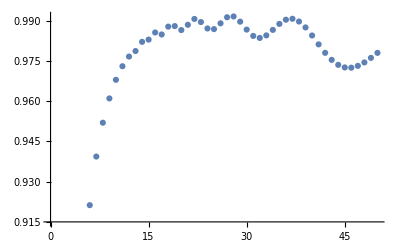

```mathematica
ListPlot[test2]
```

```mathematica
(*Analytische Integration, unbestimmt, funktioniert nicht:*)
```

```mathematica
Integrate[FavNoisy2,δBz]
```

(∫ⅇ^(-δBz^2/2) (1+Abs[Cos[1/2 π (2.2+δBz)] Cos[1/2 π √(1+(2.2+δBz)^2)]+(Cos[(π δBz)/2] Sin[1/2 π √(1+δBz^2)])/(√(1+δBz^2))+((2.2+δBz) Sin[1/2 π (2.2+δBz)] Sin[1/2 π √(1+(2.2+δBz)^2)])/(√(1+(2.2+δBz)^2))]^2)ⅆδBz)/(5 √(2 π))

```mathematica
Integrate[FavNoisy2,{δBz,-1,1}]
```

$Aborted